#### Plotting of the Legendre polynomials

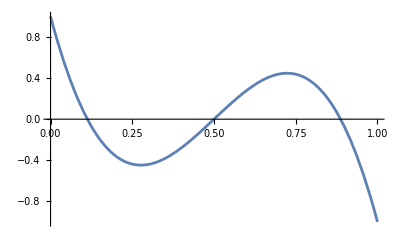

```mathematica
(* Visualization of the profiles of the Legendre polynomials *)
ϕ0[ζ_]=(-1)^0 LegendreP[0,2*ζ-1];
ϕ1[ζ_]=(-1)^1 LegendreP[1,2*ζ-1];
ϕ2[ζ_]=(-1)^2 LegendreP[2,2*ζ-1];
ϕ3[ζ_]=(-1)^3 LegendreP[3,2*ζ-1];
Plot[ϕ3[ζ],{ζ,0,1}]
```

#### Computation of the integrals

```mathematica
order=7;
```

```mathematica
(* integrals of the Legendre polynomials: (∫_0)^a Subscript[ϕ, i] dζ *)
integralValuesSingle = Table[Integrate[(-1)^i LegendreP[i,2*ζ-1],{ζ,0,a}],{i,1,order}];

(* double integrals of the Legendre polynomials: (∫_0)^a Subscript[ϕ, i] Subscript[ϕ, j] dζ *)
integralValuesDouble = Table[Integrate[(-1)^i LegendreP[i,2*ζ-1]*(-1)^j LegendreP[j,2*ζ-1],{ζ,0,a}],{i,1,order},{j,1,order}];

(* triple integrals of the Legendre polynomials: (∫_0)^a Subscript[ϕ, i] Subscript[ϕ, j] Subscript[ϕ, k] dζ *)
integralValuesTriple = Table[Integrate[(-1)^i LegendreP[i,2*ζ-1]*(-1)^j LegendreP[j,2*ζ-1]*(-1)^k LegendreP[k,2*ζ-1],{ζ,0,a}],{i,1,order},{j,1,order},{k,1,order}];
```

```mathematica
integralValuesTriple[[4,3,2]]//MatrixForm
```

a-19 a^2+186 a^3-1048 a^4+3610 a^5-7830 a^6+10720 a^7-8980 a^8+4200 a^9-840 a^10

#### Python output

Single integral

```mathematica
NumberOfEntriesSingle=order;
OutputPythonElements=ConstantArray[0,{NumberOfEntriesSingle,1}];
k=1;
For[i=1,i<=order,i++,
OutputPythonElements[[k++,1]]=integralValuesSingle[[i]];
]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"a"->"h_r","Power(a,2)"->"h_r**2","Power(a,3)"->"h_r**3","Power(a,4)"->"h_r**4","Power(a,5)"->"h_r**5","Power(a,6)"->"h_r**6","Power(a,7)"->"h_r**7","Power(a,8)"->"h_r**8","List(List("->"integrals = ","),List("->"\nintegrals = "}];
For[i=0,i <order,i++,
OutputPython=StringInsert[OutputPython,StringJoin["[",ToString[i],"]"],StringPosition[OutputPython,"integrals ",1][[1,2]]];
];
```

Double integral

```mathematica
NumberOfEntriesDouble=order*(order+1)/2;
OutputPythonElements=ConstantArray[0,{NumberOfEntriesDouble,1}];
k=1;
For[i=1,i<=order,i++,
For[j=1,j<=i,j++,
OutputPythonElements[[k++,1]]=integralValuesDouble[[i,j]];];
]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"a"->"h_r","Power(a,2)"->"h_r**2","Power(a,3)"->"h_r**3","Power(a,4)"->"h_r**4","Power(a,5)"->"h_r**5","Power(a,6)"->"h_r**6","Power(a,7)"->"h_r**7","Power(a,8)"->"h_r**8","Power(a,9)"->"h_r**9","Power(a,10)"->"h_r**10","Power(a,11)"->"h_r**11","Power(a,12)"->"h_r**12","Power(a,13)"->"h_r**13","Power(a,14)"->"h_r**14","Power(a,15)"->"h_r**15","List(List("->"integrals[] = integrals[] = ","),List("->"\nintegrals[] = integrals[] = "}];
For[i=0,i <order,i++,
For[j=0,j<i,j++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],",",ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]]];
OutputPython=StringReplace[OutputPython,{"integrals[] = "->""},1];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],",",ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
];

OutputPython
```

integrals[0,0] = h_r - 2*h_r**2 + (4*h_r**3)/3.
integrals[1,0] = integrals[0,1] = h_r - 4*h_r**2 + 6*h_r**3 - 3*h_r**4
integrals[1,1] = h_r - 6*h_r**2 + 16*h_r**3 - 18*h_r**4 + (36*h_r**5)/5.
integrals[2,0] = integrals[0,2] = h_r - 7*h_r**2 + 18*h_r**3 - 20*h_r**4 + 8*h_r**5
integrals[2,1] = integrals[1,2] = h_r - 9*h_r**2 + 36*h_r**3 - 68*h_r**4 + 60*h_r**5 - 20*h_r**6
integrals[2,2] = h_r - 12*h_r**2 + 68*h_r**3 - 190*h_r**4 + 276*h_r**5 - 200*h_r**6 + (400*h_r**7)/7.
integrals[3,0] = integrals[0,3] = h_r - 11*h_r**2 + (130*h_r**3)/3. - 80*h_r**4 + 70*h_r**5 - (70*h_r**6)/3.
integrals[3,1] = integrals[1,3] = h_r - 13*h_r**2 + 72*h_r**3 - 200*h_r**4 + 290*h_r**5 - 210*h_r**6 + 60*h_r**7
integrals[3,2] = integrals[2,3] = h_r - 16*h_r**2 + 120*h_r**3 - 460*h_r**4 + 970*h_r**5 - 1140*h_r**6 + 700*h_r**7 - 175*h_r**8
integrals[3,3] = h_r - 20*h_r**2 + (580*h_r**3)/3. - 970*h_r**4 + 2768*h_r**5 - (14000*h_r**6)/3. + 4600*h_r**7 - 2450*h_r**8 + (4900*h_r**9)/9.))

Triple integral

```mathematica
NumberOfEntriesTriple=((order+2)*(order+1)*order)/6;
OutputPythonElements=ConstantArray[0,{NumberOfEntriesTriple,1}];
k=1;
For[i=1,i<=order,i++,
For[j=1,j<=i,j++,
For[m=1,m<=j,m++,
OutputPythonElements[[k++,1]]=integralValuesTriple[[i,j,m]];
];
];
]
OutputPython = StringReplace[ToString[CForm[OutputPythonElements]],{"a"->"h_v","Power(a,2)"->"h_v**2","Power(a,3)"->"h_v**3","Power(a,4)"->"h_v**4","Power(a,5)"->"h_v**5","Power(a,6)"->"h_v**6","Power(a,7)"->"h_v**7","Power(a,8)"->"h_v**8","Power(a,9)"->"h_v**9","Power(a,10)"->"h_v**10","Power(a,11)"->"h_v**11","Power(a,12)"->"h_v**12","Power(a,13)"->"h_v**13","Power(a,14)"->"h_v**14","Power(a,15)"->"h_v**15","Power(a,16)"->"h_v**16","Power(a,17)"->"h_v**17","Power(a,18)"->"h_v**18","Power(a,19)"->"h_v**19","Power(a,20)"->"h_v**20","Power(a,21)"->"h_v**21","Power(a,22)"->"h_v**22","List(List("->"integrals[] = integrals[] = integrals[] = integrals[] = integrals[] = integrals[] = ","),List("->"\nintegrals[] = integrals[] = integrals[] = integrals[] = integrals[] = integrals[] = "}];
For[i=0,i <order,i++,
For[j=0,j<i,j++,
For[m=0,m<j,m++,
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],",",ToString[j],",",ToString[m]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],",",ToString[m],",", ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[i],",", ToString[m]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[m],",", ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[m],",",ToString[i],",", ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[m],",",ToString[j],",", ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
];
OutputPython=StringReplace[OutputPython,{"integrals[] = "->""},3];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],",",ToString[j],",",ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[i],",", ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[j],",", ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
];

For[m=0,m<j,m++,
OutputPython=StringReplace[OutputPython,{"integrals[] = "->""},3];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[j],",",ToString[m]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[j],",",ToString[m],",", ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[m],",",ToString[j],",", ToString[j]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
];

OutputPython=StringReplace[OutputPython,{"integrals[] = "->""},5];
OutputPython=StringInsert[OutputPython,StringJoin[ToString[i],",",ToString[i],",",ToString[i]],StringPosition[OutputPython,"integrals[]",1][[1,2]]];
];

OutputPython
```

integrals[0,0,0] = h_v - 3*h_v**2 + 4*h_v**3 - 2*h_v**4
integrals[1,0,0] = integrals[0,1,0] = integrals[0,0,1] = h_v - 5*h_v**2 + (34*h_v**3)/3. - 12*h_v**4 + (24*h_v**5)/5.
integrals[1,1,0] = integrals[1,0,1] = integrals[0,1,1] = h_v - 7*h_v**2 + 24*h_v**3 - 42*h_v**4 + 36*h_v**5 - 12*h_v**6
integrals[1,1,1] = h_v - 9*h_v**2 + 42*h_v**3 - 108*h_v**4 + (756*h_v**5)/5. - 108*h_v**6 + (216*h_v**7)/7.
integrals[2,0,0] = integrals[0,2,0] = integrals[0,0,2] = h_v - 8*h_v**2 + (82*h_v**3)/3. - 47*h_v**4 + 40*h_v**5 - (40*h_v**6)/3.
integrals[2,1,0] = integrals[2,0,1] = integrals[1,2,0] = integrals[1,0,2] = integrals[0,2,1] = integrals[0,1,2] = h_v - 10*h_v**2 + 48*h_v**3 - 122*h_v**4 + (844*h_v**5)/5. - 120*h_v**6 + (240*h_v**7)/7.
integrals[2,1,1] = integrals[1,2,1] = integrals[1,1,2] = h_v - 12*h_v**2 + 74*h_v**3 - 257*h_v**4 + 516*h_v**5 - 592*h_v**6 + 360*h_v**7 - 90*h_v**8
integrals[2,2,0] = integrals[2,0,2] = integrals[0,2,2] = h_v - 13*h_v**2 + 84*h_v**3 - 292*h_v**4 + 580*h_v**5 - 660*h_v**6 + 400*h_v**7 - 100*h_v**8
integrals[2,2,1] = integrals[2,1,2] = integrals[1,2,2] = h_v - 15*h_v**2 + 118*h_v**3 - 532*h_v**4 + (7164*h_v**5)/5. - 2340*h_v**6 + (15880*h_v**7)/7. - 1200*h_v**8 + (800*h_v**9)/3.
integrals[2,2,2] = h_v - 18*h_v**2 + 174*h_v**3 - 987*h_v**4 + 3420*h_v**5 - 7440*h_v**6 + 10200*h_v**7 - 8550*h_v**8 + 4000*h_v**9 - 800*h_v**10
integrals[3,0,0] = integrals[0,3,0] = integrals[0,0,3] = h_v - 12*h_v**2 + 58*h_v**3 - 145*h_v**4 + 198*h_v**5 - 140*h_v**6 + 40*h_v**7
integrals[3,1,0] = integrals[3,0,1] = integrals[1,3,0] = integrals[1,0,3] = integrals[0,3,1] = integrals[0,1,3] = h_v - 14*h_v**2 + (268*h_v**3)/3. - 308*h_v**4 + 610*h_v**5 - (2080*h_v**6)/3. + 420*h_v**7 - 105*h_v**8
integrals[3,1,1] = integrals[1,3,1] = integrals[1,1,3] = h_v - 16*h_v**2 + 126*h_v**3 - 563*h_v**4 + (7546*h_v**5)/5. - 2460*h_v**6 + (16680*h_v**7)/7. - 1260*h_v**8 + 280*h_v**9
integrals[3,2,0] = integrals[3,0,2] = integrals[2,3,0] = integrals[2,0,3] = integrals[0,3,2] = integrals[0,2,3] = h_v - 17*h_v**2 + (424*h_v**3)/3. - 640*h_v**4 + 1706*h_v**5 - (8270*h_v**6)/3. + (18580*h_v**7)/7. - 1400*h_v**8 + (2800*h_v**9)/9.
integrals[3,2,1] = integrals[3,1,2] = integrals[2,3,1] = integrals[2,1,3] = integrals[1,3,2] = integrals[1,2,3] = h_v - 19*h_v**2 + 186*h_v**3 - 1048*h_v**4 + 3610*h_v**5 - 7830*h_v**6 + 10720*h_v**7 - 8980*h_v**8 + 4200*h_v**9 - 840*h_v**10
integrals[3,2,2] = integrals[2,3,2] = integrals[2,2,3] = h_v - 22*h_v**2 + 258*h_v**3 - 1785*h_v**4 + 7674*h_v**5 - 21240*h_v**6 + (269280*h_v**7)/7. - 45300*h_v**8 + 33400*h_v**9 - 14000*h_v**10 + (28000*h_v**11)/11.
integrals[3,3,0] = integrals[3,0,3] = integrals[0,3,3] = h_v - 21*h_v**2 + 220*h_v**3 - 1260*h_v**4 + 4320*h_v**5 - 9280*h_v**6 + 12600*h_v**7 - 10500*h_v**8 + 4900*h_v**9 - 980*h_v**10
integrals[3,3,1] = integrals[3,1,3] = integrals[1,3,3] = h_v - 23*h_v**2 + (826*h_v**3)/3. - 1900*h_v**4 + 8120*h_v**5 - (67160*h_v**6)/3. + (283240*h_v**7)/7. - 47600*h_v**8 + (315700*h_v**9)/9. - 14700*h_v**10 + (29400*h_v**11)/11.
integrals[3,3,2] = integrals[3,2,3] = integrals[2,3,3] = h_v - 26*h_v**2 + (1090*h_v**3)/3. - 3015*h_v**4 + 15720*h_v**5 - 53680*h_v**6 + 123000*h_v**7 - 190350*h_v**8 + (588700*h_v**9)/3. - 129080*h_v**10 + 49000*h_v**11 - (24500*h_v**12)/3.
integrals[3,3,3] = h_v - 30*h_v**2 + 490*h_v**3 - 4805*h_v**4 + 29862*h_v**5 - 123000*h_v**6 + (2421600*h_v**7)/7. - 674100*h_v**8 + 909300*h_v**9 - 833000*h_v**10 + (5439000*h_v**11)/11. - 171500*h_v**12 + (343000*h_v**13)/13.
integrals[4,0,0] = integrals[0,4,0] = integrals[0,0,4] = h_v - 17*h_v**2 + (334*h_v**3)/3. - 380*h_v**4 + 742*h_v**5 - (2506*h_v**6)/3. + 504*h_v**7 - 126*h_v**8
integrals[4,1,0] = integrals[4,0,1] = integrals[1,4,0] = integrals[1,0,4] = integrals[0,4,1] = integrals[0,1,4] = h_v - 19*h_v**2 + 156*h_v**3 - 698*h_v**4 + 1850*h_v**5 - 2982*h_v**6 + 2868*h_v**7 - 1512*h_v**8 + 336*h_v**9
integrals[4,1,1] = integrals[1,4,1] = integrals[1,1,4] = h_v - 21*h_v**2 + 206*h_v**3 - 1148*h_v**4 + (19626*h_v**5)/5. - 8482*h_v**6 + 11592*h_v**7 - 9702*h_v**8 + 4536*h_v**9 - (4536*h_v**10)/5.
integrals[4,2,0] = integrals[4,0,2] = integrals[2,4,0] = integrals[2,0,4] = integrals[0,4,2] = integrals[0,2,4] = h_v - 22*h_v**2 + 228*h_v**3 - 1300*h_v**4 + 4450*h_v**5 - 9552*h_v**6 + 12964*h_v**7 - 10801*h_v**8 + 5040*h_v**9 - 1008*h_v**10
integrals[4,2,1] = integrals[4,1,2] = integrals[2,4,1] = integrals[2,1,4] = integrals[1,4,2] = integrals[1,2,4] = h_v - 24*h_v**2 + 286*h_v**3 - 1963*h_v**4 + 8370*h_v**5 - 23052*h_v**6 + (291496*h_v**7)/7. - 48972*h_v**8 + (108248*h_v**9)/3. - 15120*h_v**10 + (30240*h_v**11)/11.
integrals[4,2,2] = integrals[2,4,2] = integrals[2,2,4] = h_v - 27*h_v**2 + 378*h_v**3 - 3120*h_v**4 + 16218*h_v**5 - 55302*h_v**6 + 126624*h_v**7 - 195876*h_v**8 + 201880*h_v**9 - 132776*h_v**10 + 50400*h_v**11 - 8400*h_v**12
integrals[4,3,0] = integrals[4,0,3] = integrals[3,4,0] = integrals[3,0,4] = integrals[0,4,3] = integrals[0,3,4] = h_v - 26*h_v**2 + (1000*h_v**3)/3. - 2350*h_v**4 + 10040*h_v**5 - (82376*h_v**6)/3. + 49192*h_v**7 - 57470*h_v**8 + (379540*h_v**9)/9. - 17640*h_v**10 + (35280*h_v**11)/11.
integrals[4,3,1] = integrals[4,1,3] = integrals[3,4,1] = integrals[3,1,4] = integrals[1,4,3] = integrals[1,3,4] = h_v - 28*h_v**2 + 402*h_v**3 - 3325*h_v**4 + 17200*h_v**5 - 58392*h_v**6 + 133336*h_v**7 - 205954*h_v**8 + 212100*h_v**9 - 139440*h_v**10 + 52920*h_v**11 - 8820*h_v**12
integrals[4,3,2] = integrals[4,2,3] = integrals[3,4,2] = integrals[3,2,4] = integrals[2,4,3] = integrals[2,3,4] = h_v - 31*h_v**2 + 510*h_v**3 - 4980*h_v**4 + 30840*h_v**5 - 126792*h_v**6 + (2493864*h_v**7)/7. - 693840*h_v**8 + 935620*h_v**9 - 856940*h_v**10 + (5594680*h_v**11)/11. - 176400*h_v**12 + (352800*h_v**13)/13.
integrals[4,3,3] = integrals[3,4,3] = integrals[3,3,4] = h_v - 35*h_v**2 + (1990*h_v**3)/3. - 7560*h_v**4 + 55014*h_v**5 - 268042*h_v**6 + 903840*h_v**7 - 2150820*h_v**8 + (10910620*h_v**9)/3. - 4342268*h_v**10 + 3577000*h_v**11 - (5801600*h_v**12)/3. + 617400*h_v**13 - 88200*h_v**14
integrals[4,4,0] = integrals[4,0,4] = integrals[0,4,4] = h_v - 31*h_v**2 + 480*h_v**3 - 4090*h_v**4 + 21280*h_v**5 - 71904*h_v**6 + 162904*h_v**7 - 249760*h_v**8 + 255780*h_v**9 - 167580*h_v**10 + 63504*h_v**11 - 10584*h_v**12
integrals[4,4,1] = integrals[4,1,4] = integrals[1,4,4] = h_v - 33*h_v**2 + 562*h_v**3 - 5500*h_v**4 + 33840*h_v**5 - 138264*h_v**6 + 386872*h_v**7 - 751548*h_v**8 + (3035900*h_v**9)/3. - 926100*h_v**10 + (6043464*h_v**11)/11. - 190512*h_v**12 + (381024*h_v**13)/13.
integrals[4,4,2] = integrals[4,2,4] = integrals[2,4,4] = h_v - 36*h_v**2 + 690*h_v**3 - 7845*h_v**4 + 56880*h_v**5 - 276504*h_v**6 + 931224*h_v**7 - 2214450*h_v**8 + 3742900*h_v**9 - 4467680*h_v**10 + 3679704*h_v**11 - 1989204*h_v**12 + 635040*h_v**13 - 90720*h_v**14
integrals[4,4,3] = integrals[4,3,4] = integrals[3,4,4] = h_v - 40*h_v**2 + 870*h_v**3 - 11415*h_v**4 + 96126*h_v**5 - 546084*h_v**6 + 2169000*h_v**7 - 6163500*h_v**8 + 12680500*h_v**9 - 18914000*h_v**10 + (222670504*h_v**11)/11. - 15143940*h_v**12 + (97707960*h_v**13)/13. - 2222640*h_v**14 + 296352*h_v**15
integrals[4,4,4] = h_v - 45*h_v**2 + 1110*h_v**3 - 16620*h_v**4 + 160398*h_v**5 - 1050126*h_v**6 + 4844280*h_v**7 - 16155090*h_v**8 + 39553780*h_v**9 - 71555876*h_v**10 + 95393592*h_v**11 - 92468880*h_v**12 + 63345240*h_v**13 - 29053080*h_v**14 + 8001504*h_v**15 - 1000188*h_v**16
integrals[5,0,0] = integrals[0,5,0] = integrals[0,0,5] = h_v - 23*h_v**2 + (592*h_v**3)/3. - 882*h_v**4 + 2310*h_v**5 - 3682*h_v**6 + 3516*h_v**7 - 1848*h_v**8 + (1232*h_v**9)/3.
integrals[5,1,0] = integrals[5,0,1] = integrals[1,5,0] = integrals[1,0,5] = integrals[0,5,1] = integrals[0,1,5] = h_v - 25*h_v**2 + 258*h_v**3 - 1452*h_v**4 + (24654*h_v**5)/5. - 10542*h_v**6 + 14280*h_v**7 - 11886*h_v**8 + 5544*h_v**9 - (5544*h_v**10)/5.
integrals[5,1,1] = integrals[1,5,1] = integrals[1,1,5] = h_v - 27*h_v**2 + 324*h_v**3 - 2202*h_v**4 + 9306*h_v**5 - 25494*h_v**6 + 45924*h_v**7 - 53928*h_v**8 + 39704*h_v**9 - 16632*h_v**10 + 3024*h_v**11
integrals[5,2,0] = integrals[5,0,2] = integrals[2,5,0] = integrals[2,0,5] = integrals[0,5,2] = integrals[0,2,5] = h_v - 28*h_v**2 + 354*h_v**3 - 2477*h_v**4 + 10550*h_v**5 - 28812*h_v**6 + 51576*h_v**7 - 60228*h_v**8 + 44184*h_v**9 - 18480*h_v**10 + 3360*h_v**11
integrals[5,2,1] = integrals[5,1,2] = integrals[2,5,1] = integrals[2,1,5] = integrals[1,5,2] = integrals[1,2,5] = h_v - 30*h_v**2 + 428*h_v**3 - 3512*h_v**4 + (90474*h_v**5)/5. - 61312*h_v**6 + 139860*h_v**7 - 215901*h_v**8 + 222264*h_v**9 - (730464*h_v**10)/5. + 55440*h_v**11 - 9240*h_v**12
integrals[5,2,2] = integrals[2,5,2] = integrals[2,2,5] = h_v - 33*h_v**2 + 544*h_v**3 - 5272*h_v**4 + 32490*h_v**5 - 133242*h_v**6 + (2617252*h_v**7)/7. - 727608*h_v**8 + (2942072*h_v**9)/3. - 897960*h_v**10 + (5861520*h_v**11)/11. - 184800*h_v**12 + (369600*h_v**13)/13.
integrals[5,3,0] = integrals[5,0,3] = integrals[3,5,0] = integrals[3,0,5] = integrals[0,5,3] = integrals[0,3,5] = h_v - 32*h_v**2 + (1474*h_v**3)/3. - 4175*h_v**4 + 21700*h_v**5 - (219856*h_v**6)/3. + 165984*h_v**7 - 254436*h_v**8 + 260540*h_v**9 - 170688*h_v**10 + 64680*h_v**11 - 10780*h_v**12
integrals[5,3,1] = integrals[5,1,3] = integrals[3,5,1] = integrals[3,1,5] = integrals[1,5,3] = integrals[1,3,5] = h_v - 34*h_v**2 + 576*h_v**3 - 5618*h_v**4 + 34520*h_v**5 - 140952*h_v**6 + 394248*h_v**7 - 765702*h_v**8 + 1030876*h_v**9 - 943320*h_v**10 + (6155520*h_v**11)/11. - 194040*h_v**12 + (388080*h_v**13)/13.
integrals[5,3,2] = integrals[5,2,3] = integrals[3,5,2] = integrals[3,2,5] = integrals[2,5,3] = integrals[2,3,5] = h_v - 37*h_v**2 + 708*h_v**3 - 8020*h_v**4 + 58048*h_v**5 - 281952*h_v**6 + 949144*h_v**7 - 2256436*h_v**8 + 3813180*h_v**9 - 4551036*h_v**10 + 3748080*h_v**11 - 2026080*h_v**12 + 646800*h_v**13 - 92400*h_v**14
integrals[5,3,3] = integrals[3,5,3] = integrals[3,3,5] = h_v - 41*h_v**2 + (2680*h_v**3)/3. - 11680*h_v**4 + 98150*h_v**5 - (1671026*h_v**6)/3. + 2211172*h_v**7 - 6281240*h_v**8 + (116279380*h_v**9)/9. - 19268340*h_v**10 + (226820160*h_v**11)/11. - 15425200*h_v**12 + (99519000*h_v**13)/13. - 2263800*h_v**14 + 301840*h_v**15
integrals[5,4,0] = integrals[5,0,4] = integrals[4,5,0] = integrals[4,0,5] = integrals[0,5,4] = integrals[0,4,5] = h_v - 37*h_v**2 + 678*h_v**3 - 6860*h_v**4 + 42644*h_v**5 - 173964*h_v**6 + 483648*h_v**7 - 932652*h_v**8 + 1247820*h_v**9 - 1136604*h_v**10 + (7395864*h_v**11)/11. - 232848*h_v**12 + (465696*h_v**13)/13.
integrals[5,4,1] = integrals[5,1,4] = integrals[4,5,1] = integrals[4,1,5] = integrals[1,5,4] = integrals[1,4,5] = h_v - 39*h_v**2 + 776*h_v**3 - 8858*h_v**4 + 63840*h_v**5 - 308224*h_v**6 + 1032696*h_v**7 - 2447424*h_v**8 + 4128012*h_v**9 - 4921140*h_v**10 + 4050144*h_v**11 - 2188536*h_v**12 + 698544*h_v**13 - 99792*h_v**14
integrals[5,4,2] = integrals[5,2,4] = integrals[4,5,2] = integrals[4,2,5] = integrals[2,5,4] = integrals[2,4,5] = h_v - 42*h_v**2 + 928*h_v**3 - 12130*h_v**4 + 101592*h_v**5 - 575064*h_v**6 + 2279368*h_v**7 - 6469302*h_v**8 + (39899300*h_v**9)/3. - 19828200*h_v**10 + (233360064*h_v**11)/11. - 15867768*h_v**12 + (102366096*h_v**13)/13. - 2328480*h_v**14 + 310464*h_v**15
integrals[5,4,3] = integrals[5,3,4] = integrals[4,5,3] = integrals[4,3,5] = integrals[3,5,4] = integrals[3,4,5] = h_v - 46*h_v**2 + 1140*h_v**3 - 17020*h_v**4 + 163870*h_v**5 - 1071504*h_v**6 + 4939564*h_v**7 - 16466275*h_v**8 + 40305300*h_v**9 - 72902760*h_v**10 + 97177584*h_v**11 - 94190544*h_v**12 + 64521240*h_v**13 - 29591520*h_v**14 + 8149680*h_v**15 - 1018710*h_v**16
integrals[5,4,4] = integrals[4,5,4] = integrals[4,4,5] = h_v - 51*h_v**2 + 1420*h_v**3 - 24010*h_v**4 + 262710*h_v**5 - 1960266*h_v**6 + 10374076*h_v**7 - 40023480*h_v**8 + (343805420*h_v**9)/3. - 245951580*h_v**10 + (4361927472*h_v**11)/11. - 477534792*h_v**12 + (5496935640*h_v**13)/13. - 267087240*h_v**14 + 113848560*h_v**15 - 29338848*h_v**16 + (58677696*h_v**17)/17.
integrals[5,5,0] = integrals[5,0,5] = integrals[0,5,5] = h_v - 43*h_v**2 + 924*h_v**3 - 10962*h_v**4 + 80220*h_v**5 - 388164*h_v**6 + 1295112*h_v**7 - 3049536*h_v**8 + 5110308*h_v**9 - 6059340*h_v**10 + 4967424*h_v**11 - 2677752*h_v**12 + 853776*h_v**13 - 121968*h_v**14
integrals[5,5,1] = integrals[5,1,5] = integrals[1,5,5] = h_v - 45*h_v**2 + 1038*h_v**3 - 13692*h_v**4 + (571284*h_v**5)/5. - 642684*h_v**6 + 2533440*h_v**7 - 7162092*h_v**8 + 14685748*h_v**9 - (109292148*h_v**10)/5. + (256990104*h_v**11)/11. - 17463600*h_v**12 + (112620816*h_v**13)/13. - 2561328*h_v**14 + (1707552*h_v**15)/5.
integrals[5,5,2] = integrals[5,2,5] = integrals[2,5,5] = h_v - 48*h_v**2 + 1214*h_v**3 - 18107*h_v**4 + 173460*h_v**5 - 1129744*h_v**6 + 5195232*h_v**7 - 17292996*h_v**8 + 42290388*h_v**9 - 76448400*h_v**10 + 101863944*h_v**11 - 98706972*h_v**12 + 67603536*h_v**13 - 31002048*h_v**14 + 8537760*h_v**15 - 1067220*h_v**16
integrals[5,5,3] = integrals[5,3,5] = integrals[3,5,5] = h_v - 52*h_v**2 + 1458*h_v**3 - 24605*h_v**4 + 268562*h_v**5 - 2000964*h_v**6 + 10580808*h_v**7 - 40801572*h_v**8 + 116794300*h_v**9 - 250605600*h_v**10 + (4443832344*h_v**11)/11. - 486452988*h_v**12 + (5599207656*h_v**13)/13. - 272044080*h_v**14 + 115958304*h_v**15 - 29882160*h_v**16 + (59764320*h_v**17)/17.
integrals[5,5,4] = integrals[5,4,5] = integrals[4,5,5] = h_v - 57*h_v**2 + 1778*h_v**3 - 33740*h_v**4 + 415506*h_v**5 - 3503626*h_v**6 + 21063672*h_v**7 - 92937978*h_v**8 + 306962460*h_v**9 - 768344892*h_v**10 + 1465845192*h_v**11 - 2129799504*h_v**12 + 2337712776*h_v**13 - 1904673960*h_v**14 + 1115962848*h_v**15 - 444293388*h_v**16 + 107575776*h_v**17 - 11952864*h_v**18
integrals[5,5,5] = h_v - 63*h_v**2 + 2184*h_v**3 - 46242*h_v**4 + 636930*h_v**5 - 6025446*h_v**6 + 40810788*h_v**7 - 203964264*h_v**8 + 768344892*h_v**9 - 2212770420*h_v**10 + (54030663792*h_v**11)/11. - 8426123496*h_v**12 + (144760659624*h_v**13)/13. - 11224554264*h_v**14 + 8467517520*h_v**15 - 4625758368*h_v**16 + (29368186848*h_v**17)/17. - 394444512*h_v**18 + (788889024*h_v**19)/19.
integrals[6,0,0] = integrals[0,6,0] = integrals[0,0,6] = h_v - 30*h_v**2 + 328*h_v**3 - 1862*h_v**4 + (31374*h_v**5)/5. - 13272*h_v**6 + 17820*h_v**7 - 14751*h_v**8 + 6864*h_v**9 - (6864*h_v**10)/5.
integrals[6,1,0] = integrals[6,0,1] = integrals[1,6,0] = integrals[1,0,6] = integrals[0,6,1] = integrals[0,1,6] = h_v - 32*h_v**2 + (1222*h_v**3)/3. - 2817*h_v**4 + 11886*h_v**5 - 32284*h_v**6 + 57624*h_v**7 - 67188*h_v**8 + (147752*h_v**9)/3. - 20592*h_v**10 + 3744*h_v**11
integrals[6,1,1] = integrals[1,6,1] = integrals[1,1,6] = h_v - 34*h_v**2 + 492*h_v**3 - 4008*h_v**4 + (102306*h_v**5)/5. - 68880*h_v**6 + 156516*h_v**7 - 241089*h_v**8 + 247896*h_v**9 - (814176*h_v**10)/5. + 61776*h_v**11 - 10296*h_v**12
integrals[6,2,0] = integrals[6,0,2] = integrals[2,6,0] = integrals[2,0,6] = integrals[0,6,2] = integrals[0,2,6] = h_v - 35*h_v**2 + (1594*h_v**3)/3. - 4472*h_v**4 + (115694*h_v**5)/5. - (233926*h_v**6)/3. + 176400*h_v**7 - 270216*h_v**8 + 276584*h_v**9 - (905784*h_v**10)/5. + 68640*h_v**11 - 11440*h_v**12
integrals[6,2,1] = integrals[6,1,2] = integrals[2,6,1] = integrals[2,1,6] = integrals[1,6,2] = integrals[1,2,6] = h_v - 37*h_v**2 + 624*h_v**3 - 6032*h_v**4 + 36866*h_v**5 - 150114*h_v**6 + 419244*h_v**7 - 813528*h_v**8 + 1094664*h_v**9 - 1001352*h_v**10 + 593904*h_v**11 - 205920*h_v**12 + 31680*h_v**13
integrals[6,2,2] = integrals[2,6,2] = integrals[2,2,6] = h_v - 40*h_v**2 + 768*h_v**3 - 8632*h_v**4 + (310514*h_v**5)/5. - 300612*h_v**6 + (7070260*h_v**7)/7. - 2398531*h_v**8 + 4050504*h_v**9 - (24160704*h_v**10)/5. + 3978480*h_v**11 - 2150280*h_v**12 + 686400*h_v**13 - (686400*h_v**14)/7.
integrals[6,3,0] = integrals[6,0,3] = integrals[3,6,0] = integrals[3,0,6] = integrals[0,6,3] = integrals[0,3,6] = h_v - 39*h_v**2 + 706*h_v**3 - 7108*h_v**4 + 44100*h_v**5 - 179732*h_v**6 + 499408*h_v**7 - 962712*h_v**8 + 1287756*h_v**9 - 1172820*h_v**10 + 693720*h_v**11 - 240240*h_v**12 + 36960*h_v**13
integrals[6,3,1] = integrals[6,1,3] = integrals[3,6,1] = integrals[3,1,6] = integrals[1,6,3] = integrals[1,3,6] = h_v - 41*h_v**2 + (2428*h_v**3)/3. - 9188*h_v**4 + (330296*h_v**5)/5. - (955696*h_v**6)/3. + 1066632*h_v**7 - 2526792*h_v**8 + 4260716*h_v**9 - (25392156*h_v**10)/5. + 4179120*h_v**11 - 2258080*h_v**12 + 720720*h_v**13 - 102960*h_v**14
integrals[6,3,2] = integrals[6,2,3] = integrals[3,6,2] = integrals[3,2,6] = integrals[2,6,3] = integrals[2,3,6] = h_v - 44*h_v**2 + (2908*h_v**3)/3. - 12598*h_v**4 + 105200*h_v**5 - (1783856*h_v**6)/3. + 2354968*h_v**7 - 6680522*h_v**8 + (123565324*h_v**9)/9. - 20464320*h_v**10 + (240810960*h_v**11)/11. - 16372840*h_v**12 + (105618480*h_v**13)/13. - 2402400*h_v**14 + 320320*h_v**15
integrals[6,3,3] = integrals[3,6,3] = integrals[3,3,6] = h_v - 48*h_v**2 + 1192*h_v**3 - 17700*h_v**4 + 169830*h_v**5 - 1108492*h_v**6 + 5105076*h_v**7 - 17007909*h_v**8 + 41614900*h_v**9 - 75251600*h_v**10 + 100290240*h_v**11 - 97195440*h_v**12 + 66574200*h_v**13 - 30531600*h_v**14 + 8408400*h_v**15 - 1051050*h_v**16
integrals[6,4,0] = integrals[6,0,4] = integrals[4,6,0] = integrals[4,0,6] = integrals[0,6,4] = integrals[0,4,6] = h_v - 44*h_v**2 + (2818*h_v**3)/3. - 11123*h_v**4 + 81340*h_v**5 - (1180312*h_v**6)/3. + 1312416*h_v**7 - 3089844*h_v**8 + 5177372*h_v**9 - 6138480*h_v**10 + 5032104*h_v**11 - 2712556*h_v**12 + 864864*h_v**13 - 123552*h_v**14
integrals[6,4,1] = integrals[6,1,4] = integrals[4,6,1] = integrals[4,1,6] = integrals[1,6,4] = integrals[1,4,6] = h_v - 46*h_v**2 + 1056*h_v**3 - 13898*h_v**4 + (579376*h_v**5)/5. - 651504*h_v**6 + 2567544*h_v**7 - 7257294*h_v**8 + 14879292*h_v**9 - (110724072*h_v**10)/5. + (260343744*h_v**11)/11. - 17690904*h_v**12 + (114084432*h_v**13)/13. - 2594592*h_v**14 + (1729728*h_v**15)/5.
integrals[6,4,2] = integrals[6,2,4] = integrals[4,6,2] = integrals[4,2,6] = integrals[2,6,4] = integrals[2,4,6] = h_v - 49*h_v**2 + 1236*h_v**3 - 18388*h_v**4 + 175960*h_v**5 - 1145424*h_v**6 + 5265736*h_v**7 - 17524264*h_v**8 + 42850332*h_v**9 - 77453580*h_v**10 + 103196784*h_v**11 - 99994176*h_v**12 + 68483184*h_v**13 - 31404912*h_v**14 + 8648640*h_v**15 - 1081080*h_v**16
integrals[6,4,3] = integrals[6,3,4] = integrals[4,6,3] = integrals[4,3,6] = integrals[3,6,4] = integrals[3,4,6] = h_v - 53*h_v**2 + (4456*h_v**3)/3. - 25000*h_v**4 + 272510*h_v**5 - (6087242*h_v**6)/3. + 10725652*h_v**7 - 41350808*h_v**8 + (1065136900*h_v**9)/9. - 253913700*h_v**10 + (4502155584*h_v**11)/11. - 492811312*h_v**12 + (5672184504*h_v**13)/13. - 275583000*h_v**14 + 117465040*h_v**15 - 30270240*h_v**16 + (60540480*h_v**17)/17.
integrals[6,4,4] = integrals[4,6,4] = integrals[4,4,6] = h_v - 58*h_v**2 + 1812*h_v**3 - 34300*h_v**4 + 421750*h_v**5 - 3553536*h_v**6 + 21354748*h_v**7 - 94197847*h_v**8 + 311069700*h_v**9 - 778531080*h_v**10 + 1485149232*h_v**11 - 2157711696*h_v**12 + 2368242744*h_v**13 - 1929487200*h_v**14 + 1130477040*h_v**15 - 450066078*h_v**16 + 108972864*h_v**17 - 12108096*h_v**18
integrals[6,5,0] = integrals[6,0,5] = integrals[5,6,0] = integrals[5,0,6] = integrals[0,6,5] = integrals[0,5,6] = h_v - 50*h_v**2 + (3724*h_v**3)/3. - 17052*h_v**4 + (725004*h_v**5)/5. - 820064*h_v**6 + 3226440*h_v**7 - 9073122*h_v**8 + (55467964*h_v**9)/3. - (136809288*h_v**10)/5. + 29109024*h_v**11 - 21686280*h_v**12 + (139564656*h_v**13)/13. - 3171168*h_v**14 + (2114112*h_v**15)/5.
integrals[6,5,1] = integrals[6,1,5] = integrals[5,6,1] = integrals[5,1,6] = integrals[1,6,5] = integrals[1,5,6] = h_v - 52*h_v**2 + 1374*h_v**3 - 20727*h_v**4 + 198156*h_v**5 - 1283016*h_v**6 + 5865888*h_v**7 - 19436916*h_v**8 + 47381508*h_v**9 - 85468464*h_v**10 + 113724072*h_v**11 - 110101068*h_v**12 + 75365136*h_v**13 - 34550208*h_v**14 + 9513504*h_v**15 - 1189188*h_v**16
integrals[6,5,2] = integrals[6,2,5] = integrals[5,6,2] = integrals[5,2,6] = integrals[2,6,5] = integrals[2,5,6] = h_v - 55*h_v**2 + 1578*h_v**3 - 26612*h_v**4 + (1444324*h_v**5)/5. - 2142084*h_v**6 + 11291280*h_v**7 - 43454952*h_v**8 + 124233828*h_v**9 - (1331753628*h_v**10)/5. + (4720423944*h_v**11)/11. - 516534480*h_v**12 + (5943910896*h_v**13)/13. - 288742608*h_v**14 + (615317472*h_v**15)/5. - 31711680*h_v**16 + (63423360*h_v**17)/17.
integrals[6,5,3] = integrals[6,3,5] = integrals[5,6,3] = integrals[5,3,6] = integrals[3,6,5] = integrals[3,5,6] = h_v - 59*h_v**2 + (5578*h_v**3)/3. - 35168*h_v**4 + 431410*h_v**5 - (10886722*h_v**6)/3. + 21786576*h_v**7 - 96048024*h_v**8 + 317066252*h_v**9 - 793348980*h_v**10 + 1513163064*h_v**11 - 2198149856*h_v**12 + 2412421704*h_v**13 - 1965364632*h_v**14 + 1151451840*h_v**15 - 458405640*h_v**16 + 110990880*h_v**17 - 12332320*h_v**18
integrals[6,5,4] = integrals[6,4,5] = integrals[5,6,4] = integrals[5,4,6] = integrals[4,6,5] = integrals[4,5,6] = h_v - 64*h_v**2 + 2226*h_v**3 - 47033*h_v**4 + 646730*h_v**5 - 6112596*h_v**6 + 41380584*h_v**7 - 206750196*h_v**8 + 778685868*h_v**9 - 2242242240*h_v**10 + (54744852792*h_v**11)/11. - 8536880268*h_v**12 + (146655612936*h_v**13)/13. - 11371043376*h_v**14 + 8577787680*h_v**15 - 4685910768*h_v**16 + (29749747104*h_v**17)/17. - 399567168*h_v**18 + (799134336*h_v**19)/19.
integrals[6,5,5] = integrals[5,6,5] = integrals[5,5,6] = h_v - 70*h_v**2 + 2688*h_v**3 - 63042*h_v**4 + (4820634*h_v**5)/5. - 10158456*h_v**6 + 76919940*h_v**7 - 431764713*h_v**8 + 1837221372*h_v**9 - (30096583272*h_v**10)/5. + 15337313712*h_v**11 - 30546749520*h_v**12 + 47565906696*h_v**13 - 57618912384*h_v**14 + (268403191056*h_v**15)/5. - 37694976858*h_v**16 + 19286799840*h_v**17 - 6782396544*h_v**18 + 1465079616*h_v**19 - (732539808*h_v**20)/5.
integrals[6,6,0] = integrals[6,0,6] = integrals[0,6,6] = h_v - 57*h_v**2 + 1624*h_v**3 - 25592*h_v**4 + 250236*h_v**5 - 1634556*h_v**6 + 7477848*h_v**7 - 24687576*h_v**8 + 59855268*h_v**9 - 107360484*h_v**10 + 142137072*h_v**11 - 137058768*h_v**12 + 93549456*h_v**13 - 42810768*h_v**14 + 11778624*h_v**15 - 1472328*h_v**16
integrals[6,6,1] = integrals[6,1,6] = integrals[1,6,6] = h_v - 59*h_v**2 + (5326*h_v**3)/3. - 30408*h_v**4 + (1651356*h_v**5)/5. - 2437652*h_v**6 + 12777744*h_v**7 - 48940728*h_v**8 + (418239676*h_v**9)/3. - (1490677452*h_v**10)/5. + 479510136*h_v**11 - 576513168*h_v**12 + (6629104944*h_v**13)/13. - 321873552*h_v**14 + (685727328*h_v**15)/5. - 35335872*h_v**16 + (70671744*h_v**17)/17.
integrals[6,6,2] = integrals[6,2,6] = integrals[2,6,6] = h_v - 62*h_v**2 + (6022*h_v**3)/3. - 38057*h_v**4 + 464716*h_v**5 - (11671408*h_v**6)/3. + 23275728*h_v**7 - 102377916*h_v**8 + 337461428*h_v**9 - 843558504*h_v**10 + 1607866392*h_v**11 - 2334652628*h_v**12 + 2561405616*h_v**13 - 2086273728*h_v**14 + 1222107744*h_v**15 - 486491148*h_v**16 + 117786240*h_v**17 - 13087360*h_v**18
integrals[6,6,3] = integrals[6,3,6] = integrals[3,6,6] = h_v - 66*h_v**2 + 2326*h_v**3 - 49063*h_v**4 + (3360546*h_v**5)/5. - 6335504*h_v**6 + 42820624*h_v**7 - 213737724*h_v**8 + 804506652*h_v**9 - (11578146312*h_v**10)/5. + (56520017064*h_v**11)/11. - 8811828564*h_v**12 + (151355559432*h_v**13)/13. - 11734142112*h_v**14 + (44254951488*h_v**15)/5. - 4834898640*h_v**16 + (30694641120*h_v**17)/17. - 412251840*h_v**18 + (824503680*h_v**19)/19.
integrals[6,6,4] = integrals[6,4,6] = integrals[4,6,6] = h_v - 71*h_v**2 + (8218*h_v**3)/3. - 64148*h_v**4 + (4896626*h_v**5)/5. - (30923578*h_v**6)/3. + 78006096*h_v**7 - 437710536*h_v**8 + 1862103548*h_v**9 - (30499437108*h_v**10)/5. + 15540859992*h_v**11 - 30949574432*h_v**12 + 48190183272*h_v**13 - 58372437816*h_v**14 + (271904069184*h_v**15)/5. - 38185716888*h_v**16 + 19537566048*h_v**17 - 6870511648*h_v**18 + 1484106624*h_v**19 - (742053312*h_v**20)/5.
integrals[6,6,5] = integrals[6,5,6] = integrals[5,6,6] = h_v - 77*h_v**2 + (9772*h_v**3)/3. - 84252*h_v**4 + 1423506*h_v**5 - 16610538*h_v**6 + 139723452*h_v**7 - 874624104*h_v**8 + 4170046412*h_v**9 - 15398377596*h_v**10 + (489969867744*h_v**11)/11. - 101632253184*h_v**12 + (2384184343464*h_v**13)/13. - 261313784424*h_v**14 + 292085787312*h_v**15 - 252912112992*h_v**16 + (2823570664992*h_v**17)/17. - 79910262432*h_v**18 + (504463063104*h_v**19)/19. - 5441724288*h_v**20 + 518259456*h_v**21
integrals[6,6,6] = h_v - 84*h_v**2 + 3892*h_v**3 - 110558*h_v**4 + (10272906*h_v**5)/5. - 26418924*h_v**6 + 245506572*h_v**7 - 1703222667*h_v**8 + 9035930988*h_v**9 - (186541907328*h_v**10)/5. + 121395970080*h_v**11 - 313874746416*h_v**12 + 647745331464*h_v**13 - 1067802213456*h_v**14 + (7008603467184*h_v**15)/5. - 1454047747614*h_v**16 + 1175840553888*h_v**17 - 725157328896*h_v**18 + 329224319424*h_v**19 - (518324238432*h_v**20)/5. + 20212118784*h_v**21 - 1837465344*h_v**22))

```mathematica
"integrals[0,0,0] = h_v - 3*h_v**2 + 4*h_v**3 - 2*h_v**4\\nintegrals[1,0,0] = integrals[0,1,0] = integrals[0,0,1] = h_v - 5*h_v**2 + (34*h_v**3)/3. - 12*h_v**4 + (24*h_v**5)/5.\\nintegrals[1,1,0] = integrals[1,0,1] = integrals[0,1,1] = h_v - 7*h_v**2 + 24*h_v**3 - 42*h_v**4 + 36*h_v**5 - 12*h_v**6\\nintegrals[1,1,1] = h_v - 9*h_v**2 + 42*h_v**3 - 108*h_v**4 + (756*h_v**5)/5. - 108*h_v**6 + (216*h_v**7)/7.\\nintegrals[2,0,0] = integrals[0,2,0] = integrals[0,0,2] = h_v - 8*h_v**2 + (82*h_v**3)/3. - 47*h_v**4 + 40*h_v**5 - (40*h_v**6)/3.\\nintegrals[2,1,0] = integrals[2,0,1] = integrals[1,2,0] = integrals[1,0,2] = integrals[0,2,1] = integrals[0,1,2] = h_v - 10*h_v**2 + 48*h_v**3 - 122*h_v**4 + (844*h_v**5)/5. - 120*h_v**6 + (240*h_v**7)/7.\\nintegrals[2,1,1] = integrals[1,2,1] = integrals[1,1,2] = h_v - 12*h_v**2 + 74*h_v**3 - 257*h_v**4 + 516*h_v**5 - 592*h_v**6 + 360*h_v**7 - 90*h_v**8\\nintegrals[2,2,0] = integrals[2,0,2] = integrals[0,2,2] = h_v - 13*h_v**2 + 84*h_v**3 - 292*h_v**4 + 580*h_v**5 - 660*h_v**6 + 400*h_v**7 - 100*h_v**8\\nintegrals[2,2,1] = integrals[2,1,2] = integrals[1,2,2] = h_v - 15*h_v**2 + 118*h_v**3 - 532*h_v**4 + (7164*h_v**5)/5. - 2340*h_v**6 + (15880*h_v**7)/7. - 1200*h_v**8 + (800*h_v**9)/3.\\nintegrals[2,2,2] = h_v - 18*h_v**2 + 174*h_v**3 - 987*h_v**4 + 3420*h_v**5 - 7440*h_v**6 + 10200*h_v**7 - 8550*h_v**8 + 4000*h_v**9 - 800*h_v**10\\nintegrals[3,0,0] = integrals[0,3,0] = integrals[0,0,3] = h_v - 12*h_v**2 + 58*h_v**3 - 145*h_v**4 + 198*h_v**5 - 140*h_v**6 + 40*h_v**7\\nintegrals[3,1,0] = integrals[3,0,1] = integrals[1,3,0] = integrals[1,0,3] = integrals[0,3,1] = integrals[0,1,3] = h_v - 14*h_v**2 + (268*h_v**3)/3. - 308*h_v**4 + 610*h_v**5 - (2080*h_v**6)/3. + 420*h_v**7 - 105*h_v**8\\nintegrals[3,1,1] = integrals[1,3,1] = integrals[1,1,3] = h_v - 16*h_v**2 + 126*h_v**3 - 563*h_v**4 + (7546*h_v**5)/5. - 2460*h_v**6 + (16680*h_v**7)/7. - 1260*h_v**8 + 280*h_v**9\\nintegrals[3,2,0] = integrals[3,0,2] = integrals[2,3,0] = integrals[2,0,3] = integrals[0,3,2] = integrals[0,2,3] = h_v - 17*h_v**2 + (424*h_v**3)/3. - 640*h_v**4 + 1706*h_v**5 - (8270*h_v**6)/3. + (18580*h_v**7)/7. - 1400*h_v**8 + (2800*h_v**9)/9.\\nintegrals[3,2,1] = integrals[3,1,2] = integrals[2,3,1] = integrals[2,1,3] = integrals[1,3,2] = integrals[1,2,3] = h_v - 19*h_v**2 + 186*h_v**3 - 1048*h_v**4 + 3610*h_v**5 - 7830*h_v**6 + 10720*h_v**7 - 8980*h_v**8 + 4200*h_v**9 - 840*h_v**10\\nintegrals[3,2,2] = integrals[2,3,2] = integrals[2,2,3] = h_v - 22*h_v**2 + 258*h_v**3 - 1785*h_v**4 + 7674*h_v**5 - 21240*h_v**6 + (269280*h_v**7)/7. - 45300*h_v**8 + 33400*h_v**9 - 14000*h_v**10 + (28000*h_v**11)/11.\\nintegrals[3,3,0] = integrals[3,0,3] = integrals[0,3,3] = h_v - 21*h_v**2 + 220*h_v**3 - 1260*h_v**4 + 4320*h_v**5 - 9280*h_v**6 + 12600*h_v**7 - 10500*h_v**8 + 4900*h_v**9 - 980*h_v**10\\nintegrals[3,3,1] = integrals[3,1,3] = integrals[1,3,3] = h_v - 23*h_v**2 + (826*h_v**3)/3. - 1900*h_v**4 + 8120*h_v**5 - (67160*h_v**6)/3. + (283240*h_v**7)/7. - 47600*h_v**8 + (315700*h_v**9)/9. - 14700*h_v**10 + (29400*h_v**11)/11.\\nintegrals[3,3,2] = integrals[3,2,3] = integrals[2,3,3] = h_v - 26*h_v**2 + (1090*h_v**3)/3. - 3015*h_v**4 + 15720*h_v**5 - 53680*h_v**6 + 123000*h_v**7 - 190350*h_v**8 + (588700*h_v**9)/3. - 129080*h_v**10 + 49000*h_v**11 - (24500*h_v**12)/3.\\nintegrals[3,3,3] = h_v - 30*h_v**2 + 490*h_v**3 - 4805*h_v**4 + 29862*h_v**5 - 123000*h_v**6 + (2421600*h_v**7)/7. - 674100*h_v**8 + 909300*h_v**9 - 833000*h_v**10 + (5439000*h_v**11)/11. - 171500*h_v**12 + (343000*h_v**13)/13.\\nintegrals[4,0,0] = integrals[0,4,0] = integrals[0,0,4] = h_v - 17*h_v**2 + (334*h_v**3)/3. - 380*h_v**4 + 742*h_v**5 - (2506*h_v**6)/3. + 504*h_v**7 - 126*h_v**8\\nintegrals[4,1,0] = integrals[4,0,1] = integrals[1,4,0] = integrals[1,0,4] = integrals[0,4,1] = integrals[0,1,4] = h_v - 19*h_v**2 + 156*h_v**3 - 698*h_v**4 + 1850*h_v**5 - 2982*h_v**6 + 2868*h_v**7 - 1512*h_v**8 + 336*h_v**9\\nintegrals[4,1,1] = integrals[1,4,1] = integrals[1,1,4] = h_v - 21*h_v**2 + 206*h_v**3 - 1148*h_v**4 + (19626*h_v**5)/5. - 8482*h_v**6 + 11592*h_v**7 - 9702*h_v**8 + 4536*h_v**9 - (4536*h_v**10)/5.\\nintegrals[4,2,0] = integrals[4,0,2] = integrals[2,4,0] = integrals[2,0,4] = integrals[0,4,2] = integrals[0,2,4] = h_v - 22*h_v**2 + 228*h_v**3 - 1300*h_v**4 + 4450*h_v**5 - 9552*h_v**6 + 12964*h_v**7 - 10801*h_v**8 + 5040*h_v**9 - 1008*h_v**10\\nintegrals[4,2,1] = integrals[4,1,2] = integrals[2,4,1] = integrals[2,1,4] = integrals[1,4,2] = integrals[1,2,4] = h_v - 24*h_v**2 + 286*h_v**3 - 1963*h_v**4 + 8370*h_v**5 - 23052*h_v**6 + (291496*h_v**7)/7. - 48972*h_v**8 + (108248*h_v**9)/3. - 15120*h_v**10 + (30240*h_v**11)/11.\\nintegrals[4,2,2] = integrals[2,4,2] = integrals[2,2,4] = h_v - 27*h_v**2 + 378*h_v**3 - 3120*h_v**4 + 16218*h_v**5 - 55302*h_v**6 + 126624*h_v**7 - 195876*h_v**8 + 201880*h_v**9 - 132776*h_v**10 + 50400*h_v**11 - 8400*h_v**12\\nintegrals[4,3,0] = integrals[4,0,3] = integrals[3,4,0] = integrals[3,0,4] = integrals[0,4,3] = integrals[0,3,4] = h_v - 26*h_v**2 + (1000*h_v**3)/3. - 2350*h_v**4 + 10040*h_v**5 - (82376*h_v**6)/3. + 49192*h_v**7 - 57470*h_v**8 + (379540*h_v**9)/9. - 17640*h_v**10 + (35280*h_v**11)/11.\\nintegrals[4,3,1] = integrals[4,1,3] = integrals[3,4,1] = integrals[3,1,4] = integrals[1,4,3] = integrals[1,3,4] = h_v - 28*h_v**2 + 402*h_v**3 - 3325*h_v**4 + 17200*h_v**5 - 58392*h_v**6 + 133336*h_v**7 - 205954*h_v**8 + 212100*h_v**9 - 139440*h_v**10 + 52920*h_v**11 - 8820*h_v**12\\nintegrals[4,3,2] = integrals[4,2,3] = integrals[3,4,2] = integrals[3,2,4] = integrals[2,4,3] = integrals[2,3,4] = h_v - 31*h_v**2 + 510*h_v**3 - 4980*h_v**4 + 30840*h_v**5 - 126792*h_v**6 + (2493864*h_v**7)/7. - 693840*h_v**8 + 935620*h_v**9 - 856940*h_v**10 + (5594680*h_v**11)/11. - 176400*h_v**12 + (352800*h_v**13)/13.\\nintegrals[4,3,3] = integrals[3,4,3] = integrals[3,3,4] = h_v - 35*h_v**2 + (1990*h_v**3)/3. - 7560*h_v**4 + 55014*h_v**5 - 268042*h_v**6 + 903840*h_v**7 - 2150820*h_v**8 + (10910620*h_v**9)/3. - 4342268*h_v**10 + 3577000*h_v**11 - (5801600*h_v**12)/3. + 617400*h_v**13 - 88200*h_v**14\\nintegrals[4,4,0] = integrals[4,0,4] = integrals[0,4,4] = h_v - 31*h_v**2 + 480*h_v**3 - 4090*h_v**4 + 21280*h_v**5 - 71904*h_v**6 + 162904*h_v**7 - 249760*h_v**8 + 255780*h_v**9 - 167580*h_v**10 + 63504*h_v**11 - 10584*h_v**12\\nintegrals[4,4,1] = integrals[4,1,4] = integrals[1,4,4] = h_v - 33*h_v**2 + 562*h_v**3 - 5500*h_v**4 + 33840*h_v**5 - 138264*h_v**6 + 386872*h_v**7 - 751548*h_v**8 + (3035900*h_v**9)/3. - 926100*h_v**10 + (6043464*h_v**11)/11. - 190512*h_v**12 + (381024*h_v**13)/13.\\nintegrals[4,4,2] = integrals[4,2,4] = integrals[2,4,4] = h_v - 36*h_v**2 + 690*h_v**3 - 7845*h_v**4 + 56880*h_v**5 - 276504*h_v**6 + 931224*h_v**7 - 2214450*h_v**8 + 3742900*h_v**9 - 4467680*h_v**10 + 3679704*h_v**11 - 1989204*h_v**12 + 635040*h_v**13 - 90720*h_v**14\\nintegrals[4,4,3] = integrals[4,3,4] = integrals[3,4,4] = h_v - 40*h_v**2 + 870*h_v**3 - 11415*h_v**4 + 96126*h_v**5 - 546084*h_v**6 + 2169000*h_v**7 - 6163500*h_v**8 + 12680500*h_v**9 - 18914000*h_v**10 + (222670504*h_v**11)/11. - 15143940*h_v**12 + (97707960*h_v**13)/13. - 2222640*h_v**14 + 296352*h_v**15\\nintegrals[4,4,4] = h_v - 45*h_v**2 + 1110*h_v**3 - 16620*h_v**4 + 160398*h_v**5 - 1050126*h_v**6 + 4844280*h_v**7 - 16155090*h_v**8 + 39553780*h_v**9 - 71555876*h_v**10 + 95393592*h_v**11 - 92468880*h_v**12 + 63345240*h_v**13 - 29053080*h_v**14 + 8001504*h_v**15 - 1000188*h_v**16\\nintegrals[5,0,0] = integrals[0,5,0] = integrals[0,0,5] = h_v - 23*h_v**2 + (592*h_v**3)/3. - 882*h_v**4 + 2310*h_v**5 - 3682*h_v**6 + 3516*h_v**7 - 1848*h_v**8 + (1232*h_v**9)/3.\\nintegrals[5,1,0] = integrals[5,0,1] = integrals[1,5,0] = integrals[1,0,5] = integrals[0,5,1] = integrals[0,1,5] = h_v - 25*h_v**2 + 258*h_v**3 - 1452*h_v**4 + (24654*h_v**5)/5. - 10542*h_v**6 + 14280*h_v**7 - 11886*h_v**8 + 5544*h_v**9 - (5544*h_v**10)/5.\\nintegrals[5,1,1] = integrals[1,5,1] = integrals[1,1,5] = h_v - 27*h_v**2 + 324*h_v**3 - 2202*h_v**4 + 9306*h_v**5 - 25494*h_v**6 + 45924*h_v**7 - 53928*h_v**8 + 39704*h_v**9 - 16632*h_v**10 + 3024*h_v**11\\nintegrals[5,2,0] = integrals[5,0,2] = integrals[2,5,0] = integrals[2,0,5] = integrals[0,5,2] = integrals[0,2,5] = h_v - 28*h_v**2 + 354*h_v**3 - 2477*h_v**4 + 10550*h_v**5 - 28812*h_v**6 + 51576*h_v**7 - 60228*h_v**8 + 44184*h_v**9 - 18480*h_v**10 + 3360*h_v**11\\nintegrals[5,2,1] = integrals[5,1,2] = integrals[2,5,1] = integrals[2,1,5] = integrals[1,5,2] = integrals[1,2,5] = h_v - 30*h_v**2 + 428*h_v**3 - 3512*h_v**4 + (90474*h_v**5)/5. - 61312*h_v**6 + 139860*h_v**7 - 215901*h_v**8 + 222264*h_v**9 - (730464*h_v**10)/5. + 55440*h_v**11 - 9240*h_v**12\\nintegrals[5,2,2] = integrals[2,5,2] = integrals[2,2,5] = h_v - 33*h_v**2 + 544*h_v**3 - 5272*h_v**4 + 32490*h_v**5 - 133242*h_v**6 + (2617252*h_v**7)/7. - 727608*h_v**8 + (2942072*h_v**9)/3. - 897960*h_v**10 + (5861520*h_v**11)/11. - 184800*h_v**12 + (369600*h_v**13)/13.\\nintegrals[5,3,0] = integrals[5,0,3] = integrals[3,5,0] = integrals[3,0,5] = integrals[0,5,3] = integrals[0,3,5] = h_v - 32*h_v**2 + (1474*h_v**3)/3. - 4175*h_v**4 + 21700*h_v**5 - (219856*h_v**6)/3. + 165984*h_v**7 - 254436*h_v**8 + 260540*h_v**9 - 170688*h_v**10 + 64680*h_v**11 - 10780*h_v**12\\nintegrals[5,3,1] = integrals[5,1,3] = integrals[3,5,1] = integrals[3,1,5] = integrals[1,5,3] = integrals[1,3,5] = h_v - 34*h_v**2 + 576*h_v**3 - 5618*h_v**4 + 34520*h_v**5 - 140952*h_v**6 + 394248*h_v**7 - 765702*h_v**8 + 1030876*h_v**9 - 943320*h_v**10 + (6155520*h_v**11)/11. - 194040*h_v**12 + (388080*h_v**13)/13.\\nintegrals[5,3,2] = integrals[5,2,3] = integrals[3,5,2] = integrals[3,2,5] = integrals[2,5,3] = integrals[2,3,5] = h_v - 37*h_v**2 + 708*h_v**3 - 8020*h_v**4 + 58048*h_v**5 - 281952*h_v**6 + 949144*h_v**7 - 2256436*h_v**8 + 3813180*h_v**9 - 4551036*h_v**10 + 3748080*h_v**11 - 2026080*h_v**12 + 646800*h_v**13 - 92400*h_v**14\\nintegrals[5,3,3] = integrals[3,5,3] = integrals[3,3,5] = h_v - 41*h_v**2 + (2680*h_v**3)/3. - 11680*h_v**4 + 98150*h_v**5 - (1671026*h_v**6)/3. + 2211172*h_v**7 - 6281240*h_v**8 + (116279380*h_v**9)/9. - 19268340*h_v**10 + (226820160*h_v**11)/11. - 15425200*h_v**12 + (99519000*h_v**13)/13. - 2263800*h_v**14 + 301840*h_v**15\\nintegrals[5,4,0] = integrals[5,0,4] = integrals[4,5,0] = integrals[4,0,5] = integrals[0,5,4] = integrals[0,4,5] = h_v - 37*h_v**2 + 678*h_v**3 - 6860*h_v**4 + 42644*h_v**5 - 173964*h_v**6 + 483648*h_v**7 - 932652*h_v**8 + 1247820*h_v**9 - 1136604*h_v**10 + (7395864*h_v**11)/11. - 232848*h_v**12 + (465696*h_v**13)/13.\\nintegrals[5,4,1] = integrals[5,1,4] = integrals[4,5,1] = integrals[4,1,5] = integrals[1,5,4] = integrals[1,4,5] = h_v - 39*h_v**2 + 776*h_v**3 - 8858*h_v**4 + 63840*h_v**5 - 308224*h_v**6 + 1032696*h_v**7 - 2447424*h_v**8 + 4128012*h_v**9 - 4921140*h_v**10 + 4050144*h_v**11 - 2188536*h_v**12 + 698544*h_v**13 - 99792*h_v**14\\nintegrals[5,4,2] = integrals[5,2,4] = integrals[4,5,2] = integrals[4,2,5] = integrals[2,5,4] = integrals[2,4,5] = h_v - 42*h_v**2 + 928*h_v**3 - 12130*h_v**4 + 101592*h_v**5 - 575064*h_v**6 + 2279368*h_v**7 - 6469302*h_v**8 + (39899300*h_v**9)/3. - 19828200*h_v**10 + (233360064*h_v**11)/11. - 15867768*h_v**12 + (102366096*h_v**13)/13. - 2328480*h_v**14 + 310464*h_v**15\\nintegrals[5,4,3] = integrals[5,3,4] = integrals[4,5,3] = integrals[4,3,5] = integrals[3,5,4] = integrals[3,4,5] = h_v - 46*h_v**2 + 1140*h_v**3 - 17020*h_v**4 + 163870*h_v**5 - 1071504*h_v**6 + 4939564*h_v**7 - 16466275*h_v**8 + 40305300*h_v**9 - 72902760*h_v**10 + 97177584*h_v**11 - 94190544*h_v**12 + 64521240*h_v**13 - 29591520*h_v**14 + 8149680*h_v**15 - 1018710*h_v**16\\nintegrals[5,4,4] = integrals[4,5,4] = integrals[4,4,5] = h_v - 51*h_v**2 + 1420*h_v**3 - 24010*h_v**4 + 262710*h_v**5 - 1960266*h_v**6 + 10374076*h_v**7 - 40023480*h_v**8 + (343805420*h_v**9)/3. - 245951580*h_v**10 + (4361927472*h_v**11)/11. - 477534792*h_v**12 + (5496935640*h_v**13)/13. - 267087240*h_v**14 + 113848560*h_v**15 - 29338848*h_v**16 + (58677696*h_v**17)/17.\\nintegrals[5,5,0] = integrals[5,0,5] = integrals[0,5,5] = h_v - 43*h_v**2 + 924*h_v**3 - 10962*h_v**4 + 80220*h_v**5 - 388164*h_v**6 + 1295112*h_v**7 - 3049536*h_v**8 + 5110308*h_v**9 - 6059340*h_v**10 + 4967424*h_v**11 - 2677752*h_v**12 + 853776*h_v**13 - 121968*h_v**14\\nintegrals[5,5,1] = integrals[5,1,5] = integrals[1,5,5] = h_v - 45*h_v**2 + 1038*h_v**3 - 13692*h_v**4 + (571284*h_v**5)/5. - 642684*h_v**6 + 2533440*h_v**7 - 7162092*h_v**8 + 14685748*h_v**9 - (109292148*h_v**10)/5. + (256990104*h_v**11)/11. - 17463600*h_v**12 + (112620816*h_v**13)/13. - 2561328*h_v**14 + (1707552*h_v**15)/5.\\nintegrals[5,5,2] = integrals[5,2,5] = integrals[2,5,5] = h_v - 48*h_v**2 + 1214*h_v**3 - 18107*h_v**4 + 173460*h_v**5 - 1129744*h_v**6 + 5195232*h_v**7 - 17292996*h_v**8 + 42290388*h_v**9 - 76448400*h_v**10 + 101863944*h_v**11 - 98706972*h_v**12 + 67603536*h_v**13 - 31002048*h_v**14 + 8537760*h_v**15 - 1067220*h_v**16\\nintegrals[5,5,3] = integrals[5,3,5] = integrals[3,5,5] = h_v - 52*h_v**2 + 1458*h_v**3 - 24605*h_v**4 + 268562*h_v**5 - 2000964*h_v**6 + 10580808*h_v**7 - 40801572*h_v**8 + 116794300*h_v**9 - 250605600*h_v**10 + (4443832344*h_v**11)/11. - 486452988*h_v**12 + (5599207656*h_v**13)/13. - 272044080*h_v**14 + 115958304*h_v**15 - 29882160*h_v**16 + (59764320*h_v**17)/17.\\nintegrals[5,5,4] = integrals[5,4,5] = integrals[4,5,5] = h_v - 57*h_v**2 + 1778*h_v**3 - 33740*h_v**4 + 415506*h_v**5 - 3503626*h_v**6 + 21063672*h_v**7 - 92937978*h_v**8 + 306962460*h_v**9 - 768344892*h_v**10 + 1465845192*h_v**11 - 2129799504*h_v**12 + 2337712776*h_v**13 - 1904673960*h_v**14 + 1115962848*h_v**15 - 444293388*h_v**16 + 107575776*h_v**17 - 11952864*h_v**18\\nintegrals[5,5,5] = h_v - 63*h_v**2 + 2184*h_v**3 - 46242*h_v**4 + 636930*h_v**5 - 6025446*h_v**6 + 40810788*h_v**7 - 203964264*h_v**8 + 768344892*h_v**9 - 2212770420*h_v**10 + (54030663792*h_v**11)/11. - 8426123496*h_v**12 + (144760659624*h_v**13)/13. - 11224554264*h_v**14 + 8467517520*h_v**15 - 4625758368*h_v**16 + (29368186848*h_v**17)/17. - 394444512*h_v**18 + (788889024*h_v**19)/19.\\nintegrals[6,0,0] = integrals[0,6,0] = integrals[0,0,6] = h_v - 30*h_v**2 + 328*h_v**3 - 1862*h_v**4 + (31374*h_v**5)/5. - 13272*h_v**6 + 17820*h_v**7 - 14751*h_v**8 + 6864*h_v**9 - (6864*h_v**10)/5.\\nintegrals[6,1,0] = integrals[6,0,1] = integrals[1,6,0] = integrals[1,0,6] = integrals[0,6,1] = integrals[0,1,6] = h_v - 32*h_v**2 + (1222*h_v**3)/3. - 2817*h_v**4 + 11886*h_v**5 - 32284*h_v**6 + 57624*h_v**7 - 67188*h_v**8 + (147752*h_v**9)/3. - 20592*h_v**10 + 3744*h_v**11\\nintegrals[6,1,1] = integrals[1,6,1] = integrals[1,1,6] = h_v - 34*h_v**2 + 492*h_v**3 - 4008*h_v**4 + (102306*h_v**5)/5. - 68880*h_v**6 + 156516*h_v**7 - 241089*h_v**8 + 247896*h_v**9 - (814176*h_v**10)/5. + 61776*h_v**11 - 10296*h_v**12\\nintegrals[6,2,0] = integrals[6,0,2] = integrals[2,6,0] = integrals[2,0,6] = integrals[0,6,2] = integrals[0,2,6] = h_v - 35*h_v**2 + (1594*h_v**3)/3. - 4472*h_v**4 + (115694*h_v**5)/5. - (233926*h_v**6)/3. + 176400*h_v**7 - 270216*h_v**8 + 276584*h_v**9 - (905784*h_v**10)/5. + 68640*h_v**11 - 11440*h_v**12\\nintegrals[6,2,1] = integrals[6,1,2] = integrals[2,6,1] = integrals[2,1,6] = integrals[1,6,2] = integrals[1,2,6] = h_v - 37*h_v**2 + 624*h_v**3 - 6032*h_v**4 + 36866*h_v**5 - 150114*h_v**6 + 419244*h_v**7 - 813528*h_v**8 + 1094664*h_v**9 - 1001352*h_v**10 + 593904*h_v**11 - 205920*h_v**12 + 31680*h_v**13\\nintegrals[6,2,2] = integrals[2,6,2] = integrals[2,2,6] = h_v - 40*h_v**2 + 768*h_v**3 - 8632*h_v**4 + (310514*h_v**5)/5. - 300612*h_v**6 + (7070260*h_v**7)/7. - 2398531*h_v**8 + 4050504*h_v**9 - (24160704*h_v**10)/5. + 3978480*h_v**11 - 2150280*h_v**12 + 686400*h_v**13 - (686400*h_v**14)/7.\\nintegrals[6,3,0] = integrals[6,0,3] = integrals[3,6,0] = integrals[3,0,6] = integrals[0,6,3] = integrals[0,3,6] = h_v - 39*h_v**2 + 706*h_v**3 - 7108*h_v**4 + 44100*h_v**5 - 179732*h_v**6 + 499408*h_v**7 - 962712*h_v**8 + 1287756*h_v**9 - 1172820*h_v**10 + 693720*h_v**11 - 240240*h_v**12 + 36960*h_v**13\\nintegrals[6,3,1] = integrals[6,1,3] = integrals[3,6,1] = integrals[3,1,6] = integrals[1,6,3] = integrals[1,3,6] = h_v - 41*h_v**2 + (2428*h_v**3)/3. - 9188*h_v**4 + (330296*h_v**5)/5. - (955696*h_v**6)/3. + 1066632*h_v**7 - 2526792*h_v**8 + 4260716*h_v**9 - (25392156*h_v**10)/5. + 4179120*h_v**11 - 2258080*h_v**12 + 720720*h_v**13 - 102960*h_v**14\\nintegrals[6,3,2] = integrals[6,2,3] = integrals[3,6,2] = integrals[3,2,6] = integrals[2,6,3] = integrals[2,3,6] = h_v - 44*h_v**2 + (2908*h_v**3)/3. - 12598*h_v**4 + 105200*h_v**5 - (1783856*h_v**6)/3. + 2354968*h_v**7 - 6680522*h_v**8 + (123565324*h_v**9)/9. - 20464320*h_v**10 + (240810960*h_v**11)/11. - 16372840*h_v**12 + (105618480*h_v**13)/13. - 2402400*h_v**14 + 320320*h_v**15\\nintegrals[6,3,3] = integrals[3,6,3] = integrals[3,3,6] = h_v - 48*h_v**2 + 1192*h_v**3 - 17700*h_v**4 + 169830*h_v**5 - 1108492*h_v**6 + 5105076*h_v**7 - 17007909*h_v**8 + 41614900*h_v**9 - 75251600*h_v**10 + 100290240*h_v**11 - 97195440*h_v**12 + 66574200*h_v**13 - 30531600*h_v**14 + 8408400*h_v**15 - 1051050*h_v**16\\nintegrals[6,4,0] = integrals[6,0,4] = integrals[4,6,0] = integrals[4,0,6] = integrals[0,6,4] = integrals[0,4,6] = h_v - 44*h_v**2 + (2818*h_v**3)/3. - 11123*h_v**4 + 81340*h_v**5 - (1180312*h_v**6)/3. + 1312416*h_v**7 - 3089844*h_v**8 + 5177372*h_v**9 - 6138480*h_v**10 + 5032104*h_v**11 - 2712556*h_v**12 + 864864*h_v**13 - 123552*h_v**14\\nintegrals[6,4,1] = integrals[6,1,4] = integrals[4,6,1] = integrals[4,1,6] = integrals[1,6,4] = integrals[1,4,6] = h_v - 46*h_v**2 + 1056*h_v**3 - 13898*h_v**4 + (579376*h_v**5)/5. - 651504*h_v**6 + 2567544*h_v**7 - 7257294*h_v**8 + 14879292*h_v**9 - (110724072*h_v**10)/5. + (260343744*h_v**11)/11. - 17690904*h_v**12 + (114084432*h_v**13)/13. - 2594592*h_v**14 + (1729728*h_v**15)/5.\\nintegrals[6,4,2] = integrals[6,2,4] = integrals[4,6,2] = integrals[4,2,6] = integrals[2,6,4] = integrals[2,4,6] = h_v - 49*h_v**2 + 1236*h_v**3 - 18388*h_v**4 + 175960*h_v**5 - 1145424*h_v**6 + 5265736*h_v**7 - 17524264*h_v**8 + 42850332*h_v**9 - 77453580*h_v**10 + 103196784*h_v**11 - 99994176*h_v**12 + 68483184*h_v**13 - 31404912*h_v**14 + 8648640*h_v**15 - 1081080*h_v**16\\nintegrals[6,4,3] = integrals[6,3,4] = integrals[4,6,3] = integrals[4,3,6] = integrals[3,6,4] = integrals[3,4,6] = h_v - 53*h_v**2 + (4456*h_v**3)/3. - 25000*h_v**4 + 272510*h_v**5 - (6087242*h_v**6)/3. + 10725652*h_v**7 - 41350808*h_v**8 + (1065136900*h_v**9)/9. - 253913700*h_v**10 + (4502155584*h_v**11)/11. - 492811312*h_v**12 + (5672184504*h_v**13)/13. - 275583000*h_v**14 + 117465040*h_v**15 - 30270240*h_v**16 + (60540480*h_v**17)/17.\\nintegrals[6,4,4] = integrals[4,6,4] = integrals[4,4,6] = h_v - 58*h_v**2 + 1812*h_v**3 - 34300*h_v**4 + 421750*h_v**5 - 3553536*h_v**6 + 21354748*h_v**7 - 94197847*h_v**8 + 311069700*h_v**9 - 778531080*h_v**10 + 1485149232*h_v**11 - 2157711696*h_v**12 + 2368242744*h_v**13 - 1929487200*h_v**14 + 1130477040*h_v**15 - 450066078*h_v**16 + 108972864*h_v**17 - 12108096*h_v**18\\nintegrals[6,5,0] = integrals[6,0,5] = integrals[5,6,0] = integrals[5,0,6] = integrals[0,6,5] = integrals[0,5,6] = h_v - 50*h_v**2 + (3724*h_v**3)/3. - 17052*h_v**4 + (725004*h_v**5)/5. - 820064*h_v**6 + 3226440*h_v**7 - 9073122*h_v**8 + (55467964*h_v**9)/3. - (136809288*h_v**10)/5. + 29109024*h_v**11 - 21686280*h_v**12 + (139564656*h_v**13)/13. - 3171168*h_v**14 + (2114112*h_v**15)/5.\\nintegrals[6,5,1] = integrals[6,1,5] = integrals[5,6,1] = integrals[5,1,6] = integrals[1,6,5] = integrals[1,5,6] = h_v - 52*h_v**2 + 1374*h_v**3 - 20727*h_v**4 + 198156*h_v**5 - 1283016*h_v**6 + 5865888*h_v**7 - 19436916*h_v**8 + 47381508*h_v**9 - 85468464*h_v**10 + 113724072*h_v**11 - 110101068*h_v**12 + 75365136*h_v**13 - 34550208*h_v**14 + 9513504*h_v**15 - 1189188*h_v**16\\nintegrals[6,5,2] = integrals[6,2,5] = integrals[5,6,2] = integrals[5,2,6] = integrals[2,6,5] = integrals[2,5,6] = h_v - 55*h_v**2 + 1578*h_v**3 - 26612*h_v**4 + (1444324*h_v**5)/5. - 2142084*h_v**6 + 11291280*h_v**7 - 43454952*h_v**8 + 124233828*h_v**9 - (1331753628*h_v**10)/5. + (4720423944*h_v**11)/11. - 516534480*h_v**12 + (5943910896*h_v**13)/13. - 288742608*h_v**14 + (615317472*h_v**15)/5. - 31711680*h_v**16 + (63423360*h_v**17)/17.\\nintegrals[6,5,3] = integrals[6,3,5] = integrals[5,6,3] = integrals[5,3,6] = integrals[3,6,5] = integrals[3,5,6] = h_v - 59*h_v**2 + (5578*h_v**3)/3. - 35168*h_v**4 + 431410*h_v**5 - (10886722*h_v**6)/3. + 21786576*h_v**7 - 96048024*h_v**8 + 317066252*h_v**9 - 793348980*h_v**10 + 1513163064*h_v**11 - 2198149856*h_v**12 + 2412421704*h_v**13 - 1965364632*h_v**14 + 1151451840*h_v**15 - 458405640*h_v**16 + 110990880*h_v**17 - 12332320*h_v**18\\nintegrals[6,5,4] = integrals[6,4,5] = integrals[5,6,4] = integrals[5,4,6] = integrals[4,6,5] = integrals[4,5,6] = h_v - 64*h_v**2 + 2226*h_v**3 - 47033*h_v**4 + 646730*h_v**5 - 6112596*h_v**6 + 41380584*h_v**7 - 206750196*h_v**8 + 778685868*h_v**9 - 2242242240*h_v**10 + (54744852792*h_v**11)/11. - 8536880268*h_v**12 + (146655612936*h_v**13)/13. - 11371043376*h_v**14 + 8577787680*h_v**15 - 4685910768*h_v**16 + (29749747104*h_v**17)/17. - 399567168*h_v**18 + (799134336*h_v**19)/19.\\nintegrals[6,5,5] = integrals[5,6,5] = integrals[5,5,6] = h_v - 70*h_v**2 + 2688*h_v**3 - 63042*h_v**4 + (4820634*h_v**5)/5. - 10158456*h_v**6 + 76919940*h_v**7 - 431764713*h_v**8 + 1837221372*h_v**9 - (30096583272*h_v**10)/5. + 15337313712*h_v**11 - 30546749520*h_v**12 + 47565906696*h_v**13 - 57618912384*h_v**14 + (268403191056*h_v**15)/5. - 37694976858*h_v**16 + 19286799840*h_v**17 - 6782396544*h_v**18 + 1465079616*h_v**19 - (732539808*Power(h_v,20))/5.\\nintegrals[6,6,0] = integrals[6,0,6] = integrals[0,6,6] = h_v - 57*h_v**2 + 1624*h_v**3 - 25592*h_v**4 + 250236*h_v**5 - 1634556*h_v**6 + 7477848*h_v**7 - 24687576*h_v**8 + 59855268*h_v**9 - 107360484*h_v**10 + 142137072*h_v**11 - 137058768*h_v**12 + 93549456*h_v**13 - 42810768*h_v**14 + 11778624*h_v**15 - 1472328*h_v**16\\nintegrals[6,6,1] = integrals[6,1,6] = integrals[1,6,6] = h_v - 59*h_v**2 + (5326*h_v**3)/3. - 30408*h_v**4 + (1651356*h_v**5)/5. - 2437652*h_v**6 + 12777744*h_v**7 - 48940728*h_v**8 + (418239676*h_v**9)/3. - (1490677452*h_v**10)/5. + 479510136*h_v**11 - 576513168*h_v**12 + (6629104944*h_v**13)/13. - 321873552*h_v**14 + (685727328*h_v**15)/5. - 35335872*h_v**16 + (70671744*h_v**17)/17.\\nintegrals[6,6,2] = integrals[6,2,6] = integrals[2,6,6] = h_v - 62*h_v**2 + (6022*h_v**3)/3. - 38057*h_v**4 + 464716*h_v**5 - (11671408*h_v**6)/3. + 23275728*h_v**7 - 102377916*h_v**8 + 337461428*h_v**9 - 843558504*h_v**10 + 1607866392*h_v**11 - 2334652628*h_v**12 + 2561405616*h_v**13 - 2086273728*h_v**14 + 1222107744*h_v**15 - 486491148*h_v**16 + 117786240*h_v**17 - 13087360*h_v**18\\nintegrals[6,6,3] = integrals[6,3,6] = integrals[3,6,6] = h_v - 66*h_v**2 + 2326*h_v**3 - 49063*h_v**4 + (3360546*h_v**5)/5. - 6335504*h_v**6 + 42820624*h_v**7 - 213737724*h_v**8 + 804506652*h_v**9 - (11578146312*h_v**10)/5. + (56520017064*h_v**11)/11. - 8811828564*h_v**12 + (151355559432*h_v**13)/13. - 11734142112*h_v**14 + (44254951488*h_v**15)/5. - 4834898640*h_v**16 + (30694641120*h_v**17)/17. - 412251840*h_v**18 + (824503680*h_v**19)/19.\\nintegrals[6,6,4] = integrals[6,4,6] = integrals[4,6,6] = h_v - 71*h_v**2 + (8218*h_v**3)/3. - 64148*h_v**4 + (4896626*h_v**5)/5. - (30923578*h_v**6)/3. + 78006096*h_v**7 - 437710536*h_v**8 + 1862103548*h_v**9 - (30499437108*h_v**10)/5. + 15540859992*h_v**11 - 30949574432*h_v**12 + 48190183272*h_v**13 - 58372437816*h_v**14 + (271904069184*h_v**15)/5. - 38185716888*h_v**16 + 19537566048*h_v**17 - 6870511648*h_v**18 + 1484106624*h_v**19 - (742053312*Power(h_v,20))/5.\\nintegrals[6,6,5] = integrals[6,5,6] = integrals[5,6,6] = h_v - 77*h_v**2 + (9772*h_v**3)/3. - 84252*h_v**4 + 1423506*h_v**5 - 16610538*h_v**6 + 139723452*h_v**7 - 874624104*h_v**8 + 4170046412*h_v**9 - 15398377596*h_v**10 + (489969867744*h_v**11)/11. - 101632253184*h_v**12 + (2384184343464*h_v**13)/13. - 261313784424*h_v**14 + 292085787312*h_v**15 - 252912112992*h_v**16 + (2823570664992*h_v**17)/17. - 79910262432*h_v**18 + (504463063104*h_v**19)/19. - 5441724288*Power(h_v,20) + 518259456*Power(h_v,21)\\nintegrals[6,6,6] = h_v - 84*h_v**2 + 3892*h_v**3 - 110558*h_v**4 + (10272906*h_v**5)/5. - 26418924*h_v**6 + 245506572*h_v**7 - 1703222667*h_v**8 + 9035930988*h_v**9 - (186541907328*h_v**10)/5. + 121395970080*h_v**11 - 313874746416*h_v**12 + 647745331464*h_v**13 - 1067802213456*h_v**14 + (7008603467184*h_v**15)/5. - 1454047747614*h_v**16 + 1175840553888*h_v**17 - 725157328896*h_v**18 + 329224319424*h_v**19 - (518324238432*Power(h_v,20))/5. + 20212118784*Power(h_v,21) - 1837465344*Power(h_v,22)))"
```

```mathematica
integralValuesTriple[[4,1,4]]/.{a->h_v}
```

```mathematica
h_v-21 h_v^2+220 h_v^3-1260 h_v^4+4320 h_v^5-9280 h_v^6+12600 h_v^7-10500 h_v^8+4900 h_v^9-980 h_v^10
```